## BRDF Definitions

```mathematica
ggx[μ_,α_]:=α^2/(π(μ^2(α^2-1)+1)^2)
smith[θ_,α_]:=1/(Cos[θ]+√(α^2+(1-α^2)*Cos[θ]^2))
(* change[] gives cos(Subscript[θ, h]) when provided with Subscript[ω, i] and Subscript[ω, o] *)
change[θo_,θi_,ϕi_]:=(Cos[θo]+Cos[θi])/(√(2*(1+Cos[θo]*Cos[θi]+Sin[θo]*Sin[θi]*Cos[ϕi])))
oren=Function[ {θo,ϕo,θi,ϕi,α},
σ=π/2 α;
A = 1-0.5*σ^2/(σ^2+0.33);
B = 0.45*σ^2/(σ^2+0.09);
a=Max[θo,θi];
b=Min[θo,θi];
1/π(A+B*Max[0,Cos[ϕo-ϕi]]*Sin[a]*Tan[b])
];
```

## Tables Loading

### GGX

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countX=128;
countY=128;
resultEo = Import["MSBRDF_GGX_E128x128.csv","CSV"];
resultEavg=Import["MSBRDF_GGX_Eavg128.csv","CSV"];
fEo=ListInterpolation[Table[resultEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}],{{0,1},{0,1}}]
fEavg=ListInterpolation[Table[resultEavg[[i]][[2]],{i,1,countY}],{0,1}]
Plot[fEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}];
Plot3D[fEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}];

BRDFggx[θo_,θi_,ϕi_,α_]:= smith[θo,α]*smith[θi,α]*ggx[change[θo,θi,ϕi],α]
BRDFms[θo_,θi_,α_]:=((1-fEo[Cos[θo],α])*(1-fEo[Cos[θi],α]))/(π-fEavg[α])
fWhiteFurnaceSS[α_]:=2*π*NIntegrate[BRDFggx[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceMS[α_]:=2*π*NIntegrate[BRDFms[θo,θi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceSS[0.3]
fWhiteFurnaceMS[0.3]
π-fEavg[0.3]
fWhiteFurnaceSS[0.3]+fWhiteFurnaceMS[0.3]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

2.64771

0.493886

0.493886

3.14159

### Oren-Nayar

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countX=32;
countY=32;
resultOrenEo = Import["MSBRDF_OrenNayar_E32x32.csv","CSV"];
resultOrenEavg = Import["MSBRDF_OrenNayar_Eavg32.csv","CSV"];
fOrenEo=ListInterpolation[Table[resultOrenEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}],{{0,1},{0,1}}]
fOrenEavg=ListInterpolation[Table[resultOrenEavg[[i]][[2]],{i,1,countY}],{0,1}]
Plot[fOrenEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}];
Plot3D[fOrenEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}];

oren=Function[ {θo,ϕo,θi,ϕi,α},
σ=π/2 α;
A = 1-0.5*σ^2/(σ^2+0.33);
B = 0.45*σ^2/(σ^2+0.09);
a=Max[θo,θi];
b=Min[θo,θi];
1/π(A+B*Max[0,Cos[ϕo-ϕi]]*Sin[a]*Tan[b])
];
BRDForen[θo_,θi_,ϕ_,α_]:= oren[θo,0,θi,ϕ,α]
BRDForenms[θo_,θi_,ϕ_,α_]:=((1-fOrenEo[Cos[θo],α])*(1-fOrenEo[Cos[θi],α]))/(π-fOrenEavg[α])
fWhiteFurnaceSS[α_]:=2*π*NIntegrate[BRDForen[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceMS[α_]:=2*π*NIntegrate[BRDForenms[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceSS[0.3]
fWhiteFurnaceMS[0.3]
π-fOrenEavg[0.3]
fWhiteFurnaceSS[0.3]+fWhiteFurnaceMS[0.3]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

2.72499

0.416867

0.416867

3.14186

# SH Environment

We start by writing the expression we need to fit for various roughness values:

	∫_(Ω^+)^upper L(ω_i)  f(ω_o,ω_i) (ω_i· n)ⅆω  =∫_(Ω^+)^upper L(ω_i)  ((1-E(ω_o,α))(1-E(ω_i,α)))/(π-E_avg(α)) (ω_i· n)ⅆω
				=∫_(Ω^+)^upper (L_lm · Y_lm(ω_i))  ((1-E(ω_o,α))(1-E(ω_i,α)))/(π-E_avg(α)) (ω_i· n)ⅆω
				= L_lm  (1-E(ω_o,α))/(π-E_avg(α))∫_(Ω^+)^upper Y_lm(ω_i)(1-E(ω_i,α))(ω_i· n)ⅆω 
Where Y_lm(ω_i) is a spherical harmonics coefficient in the direction ω_i.
We notice that the integral is only dependent on roughness α and we will attempt to compute it for all values of (l,m) and various values of roughness to finally attempt to find a nice analytical fit for the coefficients for each BRDF.

```mathematica
SphericalPlot3D[Abs[Re[SphericalHarmonicY[1,-1,θ,ϕ]]],{θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

GGX Case

```mathematica
fSHBRDFggx= Function[ {i,θ,ϕ,α}, l=Floor[Sqrt[i]];m=i-l*(l+1); Re[SphericalHarmonicY[l,m,θ,ϕ]]*(1-fEo[Cos[θ],α])];
NIntegrate[fSHBRDFggx[2,θ,ϕ,0.5]*Cos[θ]*Sin[θ],{θ,0,π/2},{ϕ,-π,π}]
```

0.32273

```mathematica
(* Integration method & accuracy test *)
NIntegrate[fSHBRDFggx[1,θ,ϕ,α]*Cos[θ]*Sin[θ],{θ,0,π/2},{ϕ,-π,π},Method->"AdaptiveMonteCarlo",MaxRecursion->4, AccuracyGoal->4]
```

NIntegrate::inumr: The integrand 1 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}, {0, 1}}.

NIntegrate[fSHBRDFggx[1,θ,ϕ,α] Cos[θ] Sin[θ],{θ,0,π/2},{ϕ,-π,π},Method→AdaptiveMonteCarlo,MaxRecursion→4,AccuracyGoal→4]

```mathematica
α=1
Table[NIntegrate[fSHBRDFggx[i,θ,ϕ,α]*Cos[θ]*Sin[θ],{θ,0,π/2},{ϕ,-π,π},Method->"AdaptiveMonteCarlo",MaxRecursion->4, AccuracyGoal->4],{i,0,8}]
```

1

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {θ, ϕ} = {0.517343, 0.718229}. NIntegrate obtained 0.0000119017 and 0.000114672 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ, ϕ} = {0.0813497, 0.129526}. NIntegrate obtained -0.000345189 and 0.000208167 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {θ, ϕ} = {0.48099, 0.863691}. NIntegrate obtained -0.0000451148 and 0.000170332 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{0.550574,0.0000119017,0.65604,-0.000345189,-0.0000451148,0.000066622,0.35774,0.000306496,0.000154867}

Here I realized only the ZH coefficients yield non-zero values and the rest are useless! No need to bother computing all of them... :)

```mathematica
taResultSH=Table[Table[{α,NIntegrate[fSHBRDFggx[i,θ,ϕ,α]*Cos[θ]*Sin[θ],{θ,0,π/2},{ϕ,-π,π},Method->"AdaptiveMonteCarlo",MaxRecursion->4, AccuracyGoal->4]},{α,0.05,1,0.05}],{i,0,8}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ, ϕ} = {0.340685, 0.109595}. NIntegrate obtained -0.000554832 and 0.000283794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ, ϕ} = {0.147056, 0.781974}. NIntegrate obtained 0.0000933607 and 0.000147496 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ near {θ, ϕ} = {0.181869, 0.298215}. NIntegrate obtained -0.0000838108 and 0.000327622 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

{{{0.05,0.00803389},{0.1,0.0249554},{0.15,0.048202},{0.2,0.076719},{0.25,0.106963},{0.3,0.139875},{0.35,0.173263},{0.4,0.20484},{0.45,0.240272},{0.5,0.276188},{0.55,0.306383},{0.6,0.339224},{0.65,0.374436},{0.7,0.399038},{0.75,0.432664},{0.8,0.460474},{0.85,0.480315},{0.9,0.516905},{0.95,0.538752},{1.,0.554729}},{{0.05,0.0000135915},{0.1,0.0000495207},{0.15,-0.000176252},{0.2,-0.0000833229},{0.25,0.0000338425},{0.3,-0.000554832},{0.35,0.0000513818},{0.4,0.0000933607},{0.45,-0.0000792688},{0.5,0.0000622251},{0.55,-0.0000838108},{0.6,0.00129073},{0.65,0.0000181328},{0.7,9.37586×10^-6},{0.75,-0.0000540717},{0.8,-0.000605484},{0.85,0.000045988},{0.9,-0.0000591501},{0.95,0.000138969},{1.,-0.000805495}},{{0.05,0.00544379},{0.1,0.021143},{0.15,0.0459315},{0.2,0.0769586},{0.25,0.116114},{0.3,0.153371},{0.35,0.196762},{0.4,0.241322},{0.45,0.282447},{0.5,0.323757},{0.55,0.361996},{0.6,0.400319},{0.65,0.438963},{0.7,0.48508},{0.75,0.518079},{0.8,0.542746},{0.85,0.566956},{0.9,0.604622},{0.95,0.63964},{1.,0.650938}},{{0.05,-0.000240891},{0.1,0.0000431566},{0.15,0.0000658135},{0.2,-0.000216062},{0.25,0.0000317741},{0.3,0.0000932657},{0.35,0.0000652972},{0.4,-0.0000453273},{0.45,0.0000567403},{0.5,-0.0000277359},{0.55,-7.26777×10^-6},{0.6,-7.04927×10^-6},{0.65,-0.000245276},{0.7,0.000065302},{0.75,0.0000296299},{0.8,-0.0000786848},{0.85,-0.000121536},{0.9,-0.0000884674},{0.95,-0.000182793},{1.,-0.000140282}},{{0.05,-3.79945×10^-6},{0.1,0.0000218582},{0.15,-9.01891×10^-6},{0.2,0.0000536665},{0.25,-0.000116921},{0.3,-2.0512×10^-6},{0.35,0.0000133857},{0.4,0.0000947327},{0.45,-0.0000320554},{0.5,-0.0000206225},{0.55,-0.000292669},{0.6,0.0000363107},{0.65,0.0000918924},{0.7,-0.00280604},{0.75,0.000689407},{0.8,0.0000146603},{0.85,-0.0000747745},{0.9,0.000058673},{0.95,-0.0000211219},{1.,0.000114701}},{{0.05,-0.000249512},{0.1,-0.0000217539},{0.15,-0.000142801},{0.2,-0.000161343},{0.25,-0.0000955682},{0.3,0.0000581518},{0.35,0.0000518189},{0.4,0.000600356},{0.45,0.000110415},{0.5,0.0000442624},{0.55,-0.0000506063},{0.6,-0.000127692},{0.65,0.000487567},{0.7,0.000455971},{0.75,0.000042319},{0.8,-0.00109945},{0.85,-0.00176159},{0.9,0.00034021},{0.95,0.00006797},{1.,-0.000256769}},{{0.05,-0.00247041},{0.1,-0.00200003},{0.15,0.0048034},{0.2,0.0182127},{0.25,0.0369531},{0.3,0.0588998},{0.35,0.0850049},{0.4,0.111405},{0.45,0.13576},{0.5,0.162001},{0.55,0.187691},{0.6,0.214751},{0.65,0.239892},{0.7,0.257617},{0.75,0.279818},{0.8,0.298203},{0.85,0.310944},{0.9,0.321386},{0.95,0.342651},{1.,0.352601}},{{0.05,0.0000425145},{0.1,0.0000465319},{0.15,-0.000125734},{0.2,0.0002042},{0.25,-0.0000558366},{0.3,-0.0000854472},{0.35,-0.0000682334},{0.4,0.000423252},{0.45,0.000457311},{0.5,-0.000307058},{0.55,-0.00011145},{0.6,-0.000248149},{0.65,0.0000446063},{0.7,0.000364071},{0.75,0.000105225},{0.8,-0.00027471},{0.85,0.0000992759},{0.9,0.000116379},{0.95,-0.0011371},{1.,-0.0000669845}},{{0.05,0.000183892},{0.1,0.0000297379},{0.15,-6.57382×10^-7},{0.2,-0.0000146312},{0.25,0.0000455091},{0.3,-0.000105559},{0.35,0.0000105939},{0.4,-0.0000274692},{0.45,0.0000235459},{0.5,-0.00038776},{0.55,-0.0000147202},{0.6,0.000107926},{0.65,-6.02983×10^-6},{0.7,0.000206179},{0.75,0.0000405885},{0.8,-0.000436824},{0.85,-0.000297385},{0.9,0.0000100045},{0.95,-0.000216992},{1.,-0.0000481872}}}

We easily notice only the ZH coefficients are non zero, which is even better!

```mathematica
taResultSHGGX={taResultSH[[1]], taResultSH[[3]],taResultSH[[7]]}
```

{{{0.05,0.00803389},{0.1,0.0249554},{0.15,0.048202},{0.2,0.076719},{0.25,0.106963},{0.3,0.139875},{0.35,0.173263},{0.4,0.20484},{0.45,0.240272},{0.5,0.276188},{0.55,0.306383},{0.6,0.339224},{0.65,0.374436},{0.7,0.399038},{0.75,0.432664},{0.8,0.460474},{0.85,0.480315},{0.9,0.516905},{0.95,0.538752},{1.,0.554729}},{{0.05,0.00544379},{0.1,0.021143},{0.15,0.0459315},{0.2,0.0769586},{0.25,0.116114},{0.3,0.153371},{0.35,0.196762},{0.4,0.241322},{0.45,0.282447},{0.5,0.323757},{0.55,0.361996},{0.6,0.400319},{0.65,0.438963},{0.7,0.48508},{0.75,0.518079},{0.8,0.542746},{0.85,0.566956},{0.9,0.604622},{0.95,0.63964},{1.,0.650938}},{{0.05,-0.00247041},{0.1,-0.00200003},{0.15,0.0048034},{0.2,0.0182127},{0.25,0.0369531},{0.3,0.0588998},{0.35,0.0850049},{0.4,0.111405},{0.45,0.13576},{0.5,0.162001},{0.55,0.187691},{0.6,0.214751},{0.65,0.239892},{0.7,0.257617},{0.75,0.279818},{0.8,0.298203},{0.85,0.310944},{0.9,0.321386},{0.95,0.342651},{1.,0.352601}}}

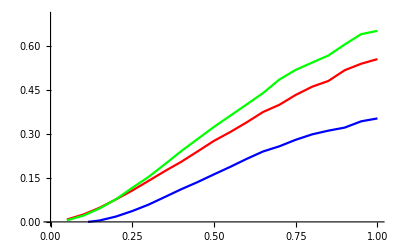

```mathematica
Show[Table[ListLinePlot[taResultSHGGX[[i]],PlotRange->{0,0.7},PlotStyle->Hue[(i-1)/3]],{i,1,3}]]
```

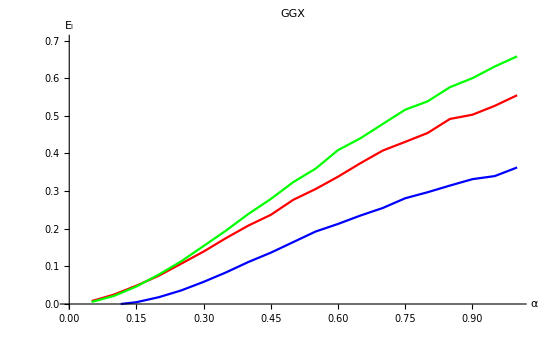

```mathematica
ZHindex={0,2,6};
taResultSHGGX=Table[Table[{α,2*π*NIntegrate[fSHBRDFggx[ZHindex[[i]],θ,0,α]*Cos[θ]*Sin[θ],{θ,0,π/2},Method->"AdaptiveMonteCarlo",MaxRecursion->8, AccuracyGoal->6]},{α,0.05,1,0.05}],{i,1,3}];
Show[Table[ListLinePlot[taResultSHGGX[[i]],PlotRange->{0,0.7},PlotStyle->Hue[(i-1)/3],AxesLabel->{"α","E_l"},PlotLabel->"GGX"],{i,1,3}]
]
```

Oren-Nayar Case

```mathematica
fSHBRDForen= Function[ {i,θ,ϕ,α}, l=Floor[Sqrt[i]];m=i-l*(l+1); Re[SphericalHarmonicY[l,m,θ,ϕ]]*(1-fOrenEo[Cos[θ],α])];
NIntegrate[fSHBRDForen[2,θ,ϕ,0.5]*Cos[θ]*Sin[θ],{θ,0,π/2},{ϕ,-π,π}]
NIntegrate[2*π*fSHBRDForen[2,θ,0,0.5]*Cos[θ]*Sin[θ],{θ,0,π/2}]
```

0.263663

0.263663

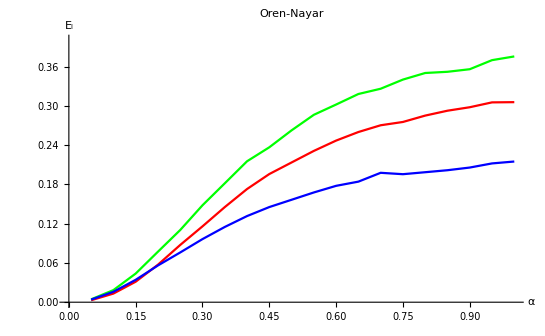

```mathematica
ZHindex={0,2,6};
taResultSHoren=Table[Table[{α,2*π*NIntegrate[fSHBRDForen[ZHindex[[i]],θ,0,α]*Cos[θ]*Sin[θ],{θ,0,π/2},Method->"AdaptiveMonteCarlo",MaxRecursion->8, AccuracyGoal->6]},{α,0.05,1,0.05}],{i,1,3}];
Show[Table[ListLinePlot[taResultSHoren[[i]],PlotRange->{0,0.4},PlotStyle->Hue[(i-1)/3],AxesLabel->{"α","E_l"},PlotLabel->"Oren-Nayar"],{i,1,3}]
]
```

## Fitting

{{a→-0.0195964,b→1.05945,c→-0.490534,d→0.},{a→-0.0641073,b→1.35195,c→-0.635011,d→0.},{a→-0.111638,b→0.891776,c→-0.420989,d→0.}}

{Function[x,-0.0195964 √x+1.05945 x^(3/2)-0.490534 x^(5/2)],Function[x,-0.0641073 √x+1.35195 x^(3/2)-0.635011 x^(5/2)],Function[x,-0.111638 √x+0.891776 x^(3/2)-0.420989 x^(5/2)]}

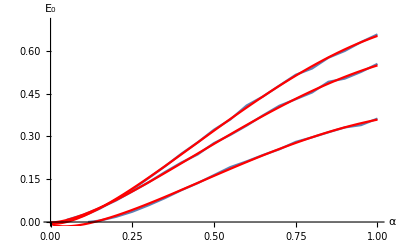

```mathematica
Clear[a,b,c,d,x]
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

model=a*(1-(b*x+c*x^2+d*x^3));
model=a*x^(1/2)+b*x^(3/2)+c*x^(5/2)+d*x^(7/2);
model=a*x^(1/2)+b*x^(3/2)+c*x^(5/2);
fitGGX=Table[FindFit[taResultSHGGX[[i]],model,{a,b,c,d},x,Method->fittingMethod],{i,1,3}]
funcSHGGX=Table[Function[x,Evaluate[model/.fitGGX[[i]]]],{i,1,3}]
Show[
Table[ListLinePlot[taResultSHGGX[[i]],PlotRange->{0,0.7},AxesLabel->{"α","E_0"}],{i,1,3}],
Table[Plot[funcSHGGX[[i]][x],{x,0,1},PlotStyle->Red],{i,1,3}]
]
```

{{a→-0.0975902,b→1.51006,c→-1.74744,d→0.641786},{a→-0.109412,b→1.86291,c→-2.23023,d→0.850618},{a→-0.0427041,b→1.10096,c→-1.42818,d→0.585121}}

{Function[x,-0.0975902 √x+1.51006 x^(3/2)-1.74744 x^(5/2)+0.641786 x^(7/2)],Function[x,-0.109412 √x+1.86291 x^(3/2)-2.23023 x^(5/2)+0.850618 x^(7/2)],Function[x,-0.0427041 √x+1.10096 x^(3/2)-1.42818 x^(5/2)+0.585121 x^(7/2)]}

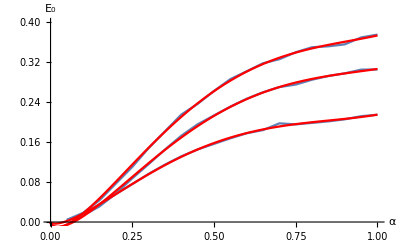

```mathematica
model=0*a+b*x+c*x^2+d*x^3+e*x^4;
model=a*x^(1/2)+b*x^(3/2)+c*x^(5/2)+d*x^(7/2);
fitOren=Table[FindFit[taResultSHoren[[i]],model,{a,b,c,d},x,Method->fittingMethod],{i,1,3}]
funcSHOren=Table[Function[x,Evaluate[model/.fitOren[[i]]]],{i,1,3}]
Show[
Table[ListLinePlot[taResultSHoren[[i]],PlotRange->{0,0.4},AxesLabel->{"α","E_0"}],{i,1,3}],
Table[Plot[funcSHOren[[i]][x],{x,0,1},PlotStyle->Red],{i,1,3}]
]
```

```mathematica
{a->-0.0919559140506979,b->1.467037714315657,c->-1.6735448883797404,d->0.607800523815945},{a->-0.11366841288600084,b->1.901273744271233,c->-2.322322430339633,d->0.909815621695672},{a->-0.04124821752212919,b->1.0933549500536324,c->-1.4171919237898756,d->0.5810844359893627}
```